### A

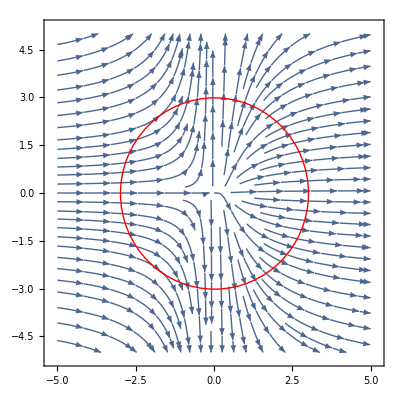

```mathematica
stream = StreamPlot[{x^2, y}, {x,-5,5},{y,-5,5}];
circle = Graphics[{Red,Circle[{0,0},3]}];
Show[{stream, circle}]
```

### B

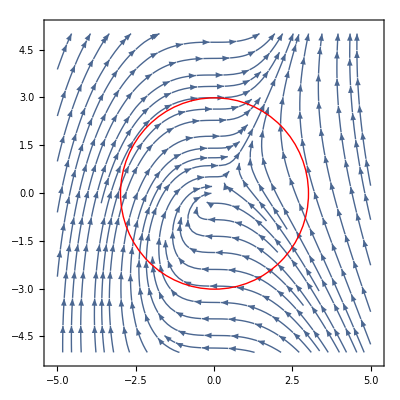

```mathematica
stream = StreamPlot[{y-x, x^2}, {x,-5,5},{y,-5,5}];
circle = Graphics[{Red,Circle[{0,0},3]}];
Show[{stream, circle}]
```

### C

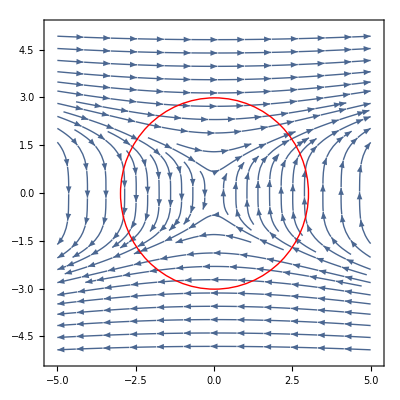

```mathematica
stream = StreamPlot[{y^3, x}, {x,-5,5},{y,-5,5}];
circle = Graphics[{Red,Circle[{0,0},3]}];
Show[{stream, circle}]
```

### D

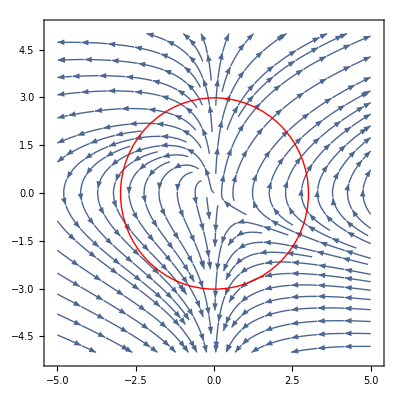

```mathematica
stream = StreamPlot[{x y, x+y}, {x,-5,5},{y,-5,5}];
circle = Graphics[{Red,Circle[{0,0},3]}];
Show[{stream, circle}]
```

### Creation mode

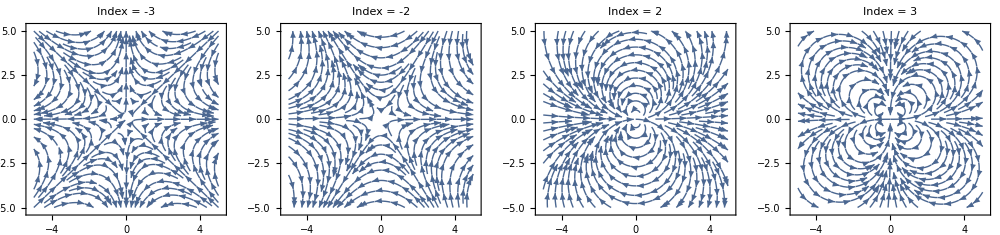

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/Constructed.png

```mathematica
CreateFunc[x_,y_,n_] = (x+I y)^n;
tab = Table[{StreamPlot[{Re[CreateFunc[x,y,n]],Im[CreateFunc[x,y,n]]},{x,-5,5},{y,-5,5}, PlotLabel->StringForm["Index  = ``", n]],StringForm["ẋ=`` \n ẏ=``",Re[CreateFunc[x,y,n]] //ComplexExpand,Im[CreateFunc[x,y,n]]//ComplexExpand]},{n,{-3,-2,2,3}}];
g = GraphicsGrid[Transpose[tab], ImageSize->1000]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/Constructed.png",g,"PNG"]
```